```mathematica
rper:=0.7Rsun;
θper:=45*Pi/180;
Rper:=rper*Cos[θper];
zper:=rper*Sin[θper];

Mu=0.62;
γ=5/3;
ν=23;
kRoss=21.1; (* Rosseland opacity at 0.7 Rsun*)
χ=10^3*(16*T[Rper,zper]^3*sigmaSB*(γ-1)*Mu*mP)/(3*kRoss*ρ[Rper,zper]^2*kB)   (*this is what Goldreich and Schubert call χ*)
ξradiative = (γ-1)*χ   (*this is what Balbus and Schaan call ξrad*)
η=596;
```

2.13929×10^10

1.42619×10^10

```mathematica
NMaxIterations=70;
tEnd=3*10^8;
tref=1/Ω[Rper,zper];
```

```mathematica
kR0:=-10^-4.5;
kϕ0=10^-7;
kz0:=10^-7;

kR[t_]:=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]:=kϕ0;
kz[t_]:=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;
```

```mathematica
CreateElement
```

{{{-0.0000316228,1/10000000,1/10000000},{0.00316228,0,1},{37256.6,{t→6.23512×10^7}}}}

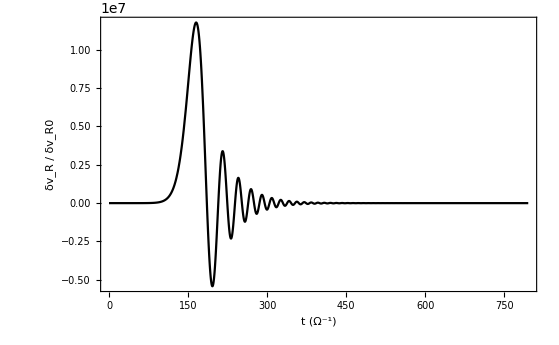

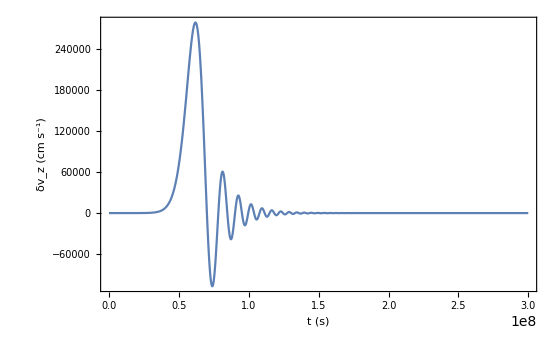

```mathematica
δvRPlot=Plot[δvRsol[t*tref]/δvRsol[0],{t,0,(tEnd/tref)},PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv_R / δv_R0 ","ξ_rad = 10^3 ξ_(rad⊙),  ν = ν_⊙"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotStyle->Black,LabelStyle->Black]
Plot[δvzsol[t]/δvzsol[0],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δv_z (cm s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->12}]
Plot[δCRsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δC_R (gauss)"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
Plot[δCzsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δC_z (gauss)"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
Plot[δρsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δρ (g cm^-3)"},BaseStyle->{FontWeight->"Bold",FontSize->12}];
```

```mathematica
SoluzioniGS2=Select[Table[{temp,Ω[Rper,zper]*q/.NSolve[DispersionRelationGS/.{t->temp*tref},q][[3]]},{temp,0,tEnd/tref,(tEnd/tref)/(2*10^3)}],Re[#[[2]]]>0&];
```

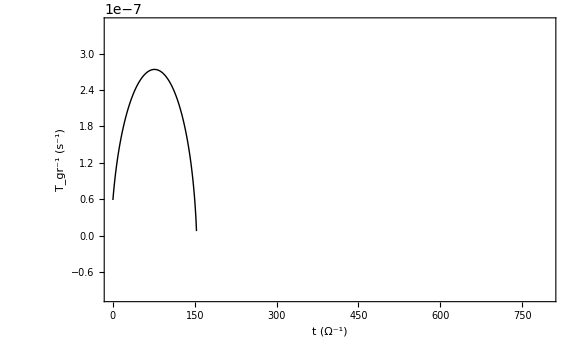

```mathematica
NuGrowthPlot=ListPlot[SoluzioniGS2,Frame->True,FrameLabel->{"t (Ω^-1)","T_gr^-1 (s^-1)","ξ_rad = 10^3 ξ_(rad⊙), ν = ν_⊙"},LabelStyle->Black,BaseStyle->{FontWeight->"Bold",FontSize->12},PlotRange->{{0,tEnd/tref},{-10^-7,3.5*10^-7}},Joined->True,PlotStyle->Directive[Thick,Black]]
```

```mathematica
TGrowthPlotat45withνReduced=ListContourPlot[TgrowthkRkzTable,PlotRange->{{-9,-3},{-9,-3}},PlotLegends->BarLegend[Automatic,LegendMarkerSize->200,LegendFunction->"Frame",LegendMargins->4,LegendLabel->"Log_10(T_gr/s)",LabelStyle->{FontSize->12}],FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R < 0, k_z > 0, ξ_rad = 10^3 ξ_(rad⊙), ν = ν_⊙"},Contours->{6.7,7,8,9,10,11,12},ContourLabels->None,ContourStyle->Thick,BaseStyle->{FontWeight->"Bold",FontSize->12,FontColor->Brown}];
Manipulate[Show[R2at45withνSmaller,TGrowthPlotat45withνReduced,Graphics[{PointSize[Large],Red,Point[{Log10[Abs[kR[t]]],Log10[Abs[kz[t]]]}]}]],{t,0,tEnd}];
```

```mathematica
kCoordinates[t_]={Log10[Abs[kR[t]]],Log10[Abs[kz[t]]]};
InitialPoint=Point[kCoordinates[0]];
FinalPoint=Point[kCoordinates[tEnd]];
kPositionPlotTemp=Show[R2at45withνSmaller,TGrowthPlotat45withν,Graphics[{PointSize[Large],Red,InitialPoint,FinalPoint,Thick,Line[{kCoordinates[0],kCoordinates[tEnd]}]}]];
```

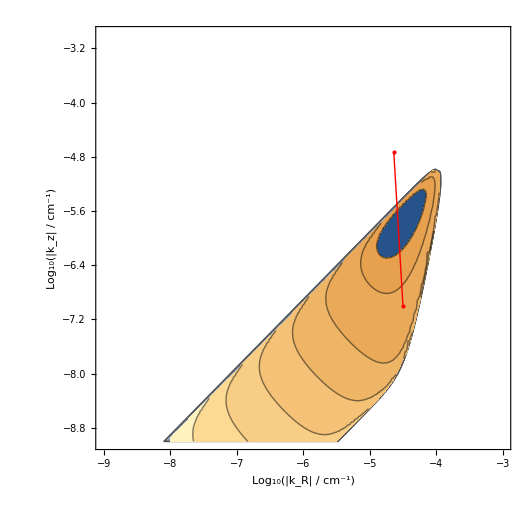
```mathematica
kPositionPlot=-Graphics-
```

```mathematica
(*Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\GoldreichSchubert - Revisited\\GS - Model A - Higher Thermal Diffusion\\picGS4.png",δvRPlot,ImageResolution->150];
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\GoldreichSchubert - Revisited\\GS - Model A - Higher Thermal Diffusion\\picGS5.png",kPositionPlot,ImageResolution->150];
Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\GoldreichSchubert - Revisited\\GS - Model A - Higher Thermal Diffusion\\picGS6.png",NuGrowthPlot,ImageResolution->150];*)
```